# Анимация в Mathematica на примере курсовой работы по теоретической механике

Юдинцев В. В. 
Кафедра теоретической механики
Самарский университет

Стили по умолчанию...

```mathematica
SetOptions[Graphics,BaseStyle->{14,FontFamily->"Helvetica"}];
```

## Геометрические объекты в Mathematica

Окружность



```mathematica
Graphics[Circle[{0,0},2]]
```

## Геометрические объекты в Mathematica

Круг или диск



```mathematica
Graphics[Disk[{0,0},2]]
```

## Несколько объектов

Несколько объектов {g_1, g_2, g_3, ..., g_n}

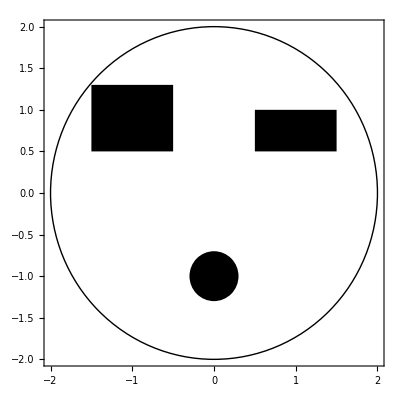

```mathematica
Graphics[{
Circle[{0, 0}, 2],
Rectangle[{0.5, 0.5},{1.5,1}],
Rectangle[{-1.5, 0.5},{-0.5,1.3}],
Disk[{0, -1},0.3]
},
Frame->True]
```

## Контур и заливка

Заливка

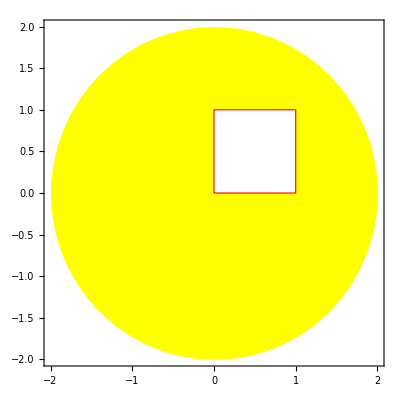

```mathematica
Graphics[{
Yellow,Disk[{0, 0}, 2],
White,EdgeForm[{Thick,Red,Dashed}],Rectangle[{0, 0},{1,1}]
},
Frame->True]
```

## Сектор

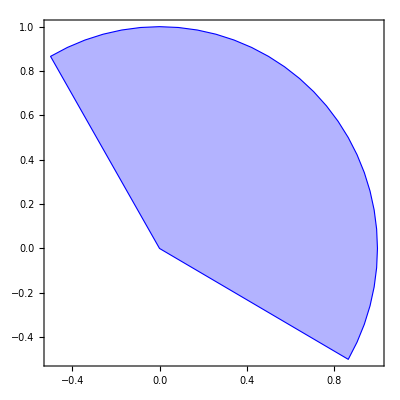

```mathematica
Graphics[{
Lighter[Blue,0.7],
EdgeForm[{Thick,Blue}],
Disk[{0,0},1,{-30°,120°}]},
Frame->True]
```

Угол отсчитывается от горизонтальной оси против часовой стрелки

## Тело 1 механизма

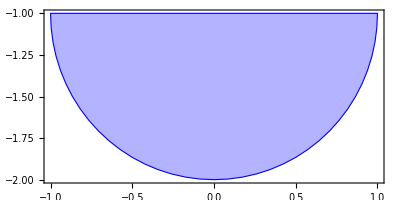

```mathematica
Graphics[{
Lighter[Blue,0.7],
EdgeForm[{Thick,Blue}],
Disk[{0,-1},1,{-180°,0°}]},
Frame->True]
```

## Опора

Функция Line[{{x1,y1},{x2,y2},{x3,y3}}]

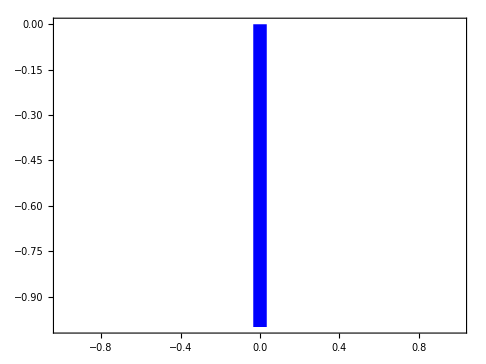

```mathematica
Graphics[{
Blue,Thickness[0.02],
Line[{{0,0},{0,-1}}]
},Frame->True]
```

## Стойка, стержень и диск

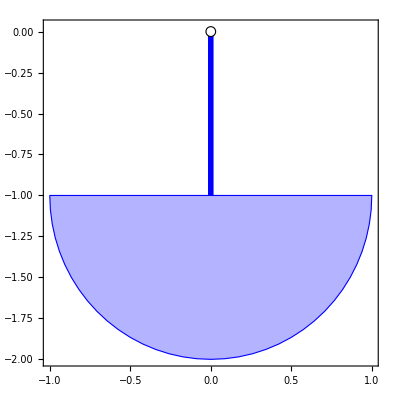

```mathematica
Graphics[{
(* Стержень *)
Blue,Thickness[0.01],Line[{{0,0},{0,-1}}],
(* Стойка *)
White,EdgeForm[{Thick,Black}],Disk[{0,0},0.03],
(* Диск *)
Lighter[Blue,0.7],EdgeForm[{Thick,Blue}],Disk[{0,-1},1,{-180°,0°}]
},Frame->True]
```

## Стойка, стержень и диск

Объединяем в список геометрических объектов, с которым в дальнейшем будем работать, как с единым объектом

```mathematica
body1={
Blue,Thickness[0.01],Line[{{0,0},{0,-1}}],

Lighter[Blue,0.7],EdgeForm[{Thick,Blue}],
Disk[{0,-1},1,{-180°,0°}],

White,EdgeForm[{Thick,Black}],
Disk[{0,0},0.03]
}
```

{RGBColor[0, 0, 1],Thickness[0.01],Line[{{0,0},{0,-1}}],RGBColor[0.7, 0.7, 1.],EdgeForm[{Thickness[Large],RGBColor[0, 0, 1]}],Disk[{0,-1},1,{-180 °,0}],GrayLevel[1],EdgeForm[{Thickness[Large],GrayLevel[0]}],Disk[{0,0},0.03]}

Чтобы показать эти объекты необходимо использовать функцию Graphics[]

## Перемещение и поворот

Графический комплекс, состоящий из стойки и пластины

```mathematica
Graphics[body1,Frame->True]
```

-Graphics-

## Перемещение и поворот

Перенесём объект на 1 и 1 вдоль осей x и y

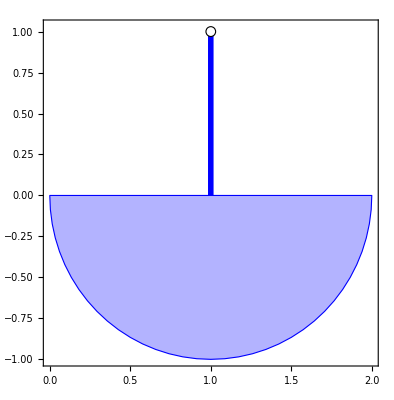

```mathematica
Graphics[
GeometricTransformation[body1,{RotationMatrix[0],{1,1}}],
Frame->True]
```

## Матрица поворота

Матрица поворота в плоскости

(x'
y')=(cos φ | -sin φ
cos φ | cos φ)·(x
y)

Точка с координатами (x
y) поворачивается на угол φ вокруг начала координат

```mathematica
RotationMatrix[45.0°]//MatrixForm
```

(0.707107 | -0.707107
0.707107 | 0.707107)

Поворачиваем вектор {1, 0} на 20 градусов против часовой стрелки

```mathematica
RotationMatrix[20.0 °].{1,0}
```

{0.939693,0.34202}

## Поворот вектора

Исходный вектор

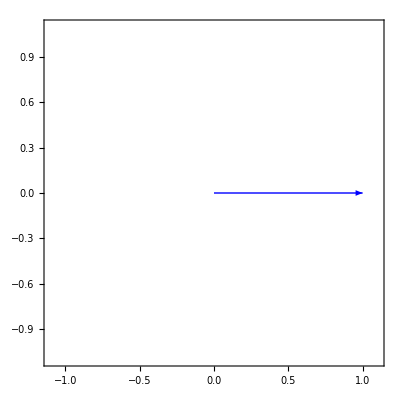

```mathematica
r1={1.0,0.0};
Graphics[{
Blue,Arrow[{{0,0},r1}]
},
PlotRange->{{-1.1,1.1},{-1.1,1.1}},Frame->True]
```

## Поворот вектора

Повернутый вектор

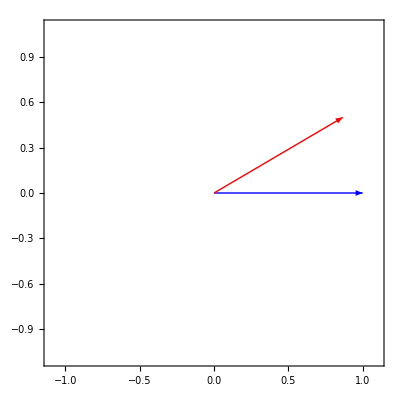

```mathematica
Graphics[{
Blue,Arrow[{{0, 0},r1}],
Red,Arrow[{{0, 0},RotationMatrix[30°]. r1}]
  },
PlotRange->{{-1.1,1.1},{-1.1,1.1}},Frame->True]
```

Это “активная” точка зрения на поворот - поворачивается объект.

## GeometricTransformation

Использование функции GeometricTransformation для поворота и перемещения

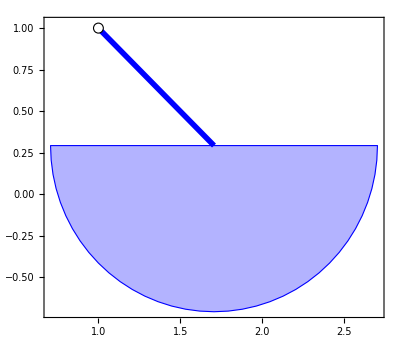

```mathematica
Graphics[
GeometricTransformation[body1,{RotationMatrix[45°],{1,1}}],
Frame->True]
```

## Держимся в рамках

Опция PlotRange позволяет определить границы область рисунка

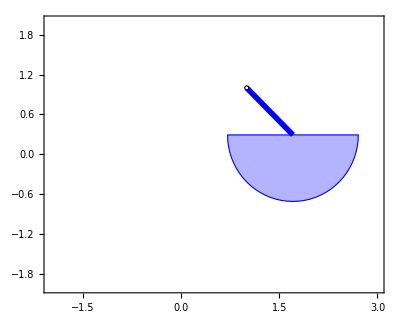

```mathematica
Graphics[
GeometricTransformation[body1,{RotationMatrix[45°],{1,1}}],
Frame->True,PlotRange->{{-2,3},{-2,2}}]
```

## Объект как функция положения

Создадим функцию, для формирования геометрического объекта в заданном положении. Удалим все определения, связанные с именем body1:

```mathematica
ClearAll[body1];
```

Определяем функцию от угла поворота с именем body

```mathematica
body1[φ_]:=Module[{b},
b={
(* Стержень *)
Blue,Thickness[0.01],Line[{{0,0},{0,-1}}],
(* Сектор, пластина *)
Lighter[Blue,0.7],EdgeForm[Directive[Thick,Blue]],
Disk[{0,-1},1,{-180°,0°}],
(* Стойка *)
White,EdgeForm[Directive[Thick,Black]],
Disk[{0,0},0.03]
};
GeometricTransformation[b,{RotationMatrix[φ],{0,0}}]
];
```

Функция Module позволяет создавать многострочные функции с локальными переменными, как в традиционных языках программирования.

## Поворот

Рисуем, вызывая новую функцию

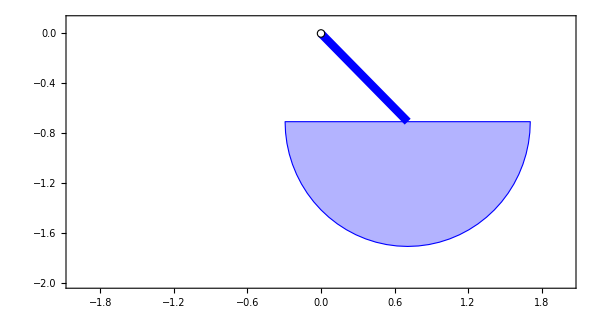

```mathematica
Graphics[body1[45°],Frame->True,PlotRange->{{-2,2},{-2,0.1}},ImageSize->600]
```

## Добавляем канал для шарика

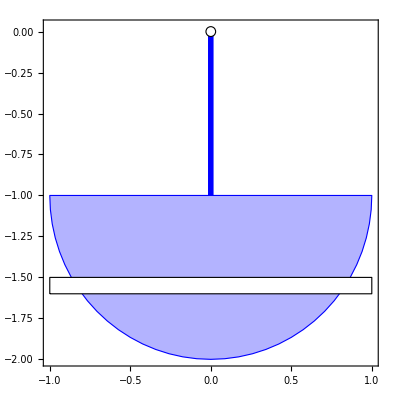

```mathematica
body1[φ_]:=Module[{b},
b={
(* Стержень *)
Blue,Thickness[0.01],Line[{{0,0},{0,-1}}],
(* Сектор, пластина *)
Lighter[Blue,0.7],EdgeForm[Directive[Thick,Blue]],
Disk[{0,-1},1,{-180°,0°}],
(* Стойка *)
White,EdgeForm[Directive[Thick,Black]],
Disk[{0,0},0.03],
(* Канал *)
 Rectangle[{-1, -1.6}, {1, -1.5}]
};
GeometricTransformation[b,{RotationMatrix[φ],{0,0}}]
];

Graphics[body1[0°],Frame->True]
```

## Канал для шарика

Маскируем (убираем границу у всех объектов), чтобы казалось, что пластина с каналом это единый объект.

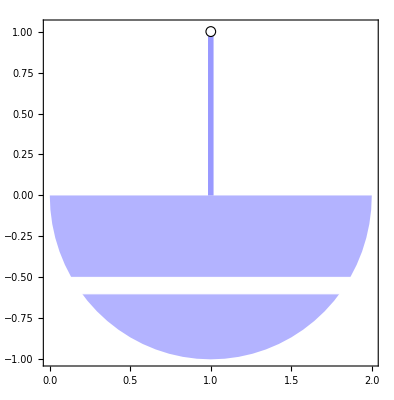

```mathematica
body1[φ_] := Module[{b},
   b = {
     Lighter[Blue, 0.6],Thickness[0.01],Line[{{0, 0}, {0, -1}}],
     
     Lighter[Blue, 0.7],
     Disk[{0, -1}, 1, {-180 °, 0 °}],
     
     White, EdgeForm[Directive[Thick, Black]],
     Disk[{0, 0}, 0.03],

     EdgeForm[Directive[Thin, White]],
     Rectangle[{-1, -1.6}, {1, -1.5}]
     };
   GeometricTransformation[b, {RotationMatrix[φ], {1, 1}}]
   ];
Graphics[body1[0 °], Frame -> True]
```

## Пружина

Функция Table генерирует списки
Table[выражение, {i, начальное значение, конечное значение, шаг}]

```mathematica
Table[i^2,{i,0,5}]
```

{0,1,4,9,16,25}

```mathematica
Table[{i,i^2},{i,0,5}]
```

{{0,0},{1,1},{2,4},{3,9},{4,16},{5,25}}

Пружина в виде ломаной линии

```mathematica
Spring[L_,d_,n_]:=Table[{i *L/n,(-1)^i d/2},{i,0,n}];
Spring[0.5,0.01,5]
```

{{0.,0.005},{0.1,-0.005},{0.2,0.005},{0.3,-0.005},{0.4,0.005},{0.5,-0.005}}

Чтобы нарисовать пружину, используем 
функцию Line[{p1, p2, p3,..., pn}]

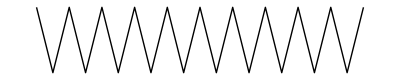

```mathematica
Graphics[
Line[Spring[0.5, 0.01, 20]]
]
```

Больше “витков”, больше диаметр

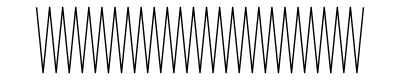

```mathematica
Graphics[
 Line[Spring[0.5, 0.03, 50]]
 ]
```

## Перемещение и поворот пружины

Линию, нарисованную по точкам, тоже можно поворачивать и перемещать, используя функцию GeometricTransformation

Поворачиваем на 20 градусов и перемещаем на 1 и 1 по x и y соответственно

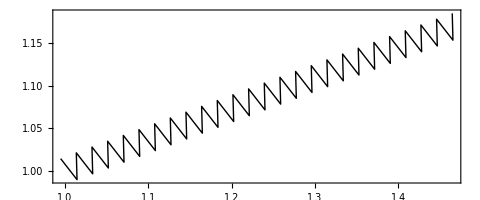

```mathematica
Graphics[
GeometricTransformation[Line[Spring[0.5, 0.03, 50]],{RotationMatrix[20°], {1, 1}}],
Frame->True
  ]
```

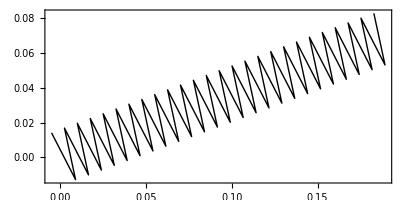

```mathematica
Graphics[
 GeometricTransformation[Line[Spring[0.2, 0.03, 50]],{RotationMatrix[20 °], {0, 0}}],
Frame -> True
]
```

## Стержень, пластина и пружина

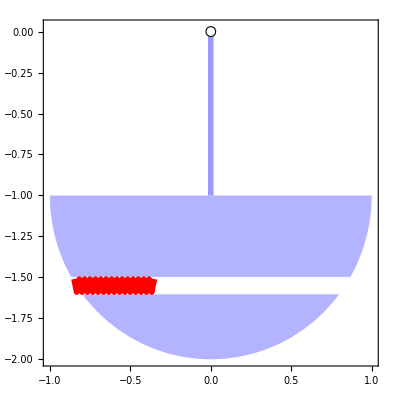

```mathematica
body1[φ_] := Module[{b},
b=
{
Lighter[Blue, 0.6],Thickness[0.01],Line[{{0, 0}, {0, -1}}],

Lighter[Blue, 0.7],Disk[{0, -1}, 1, {-180 °, 0 °}],

White, EdgeForm[{Thick, Black}],
Disk[{0, 0}, 0.03],

EdgeForm[{Thin, White}],
Rectangle[{-1, -1.6}, {1, -1.5}],

Red,Thin,Translate[Line[Spring[0.5, 0.08, 30]],{-0.85,-1.55}]}
;
   GeometricTransformation[b, {RotationMatrix[φ], {0, 0}}]
   ];
Graphics[body1[0 °],Frame -> True]
```

## Шарик

Добавляем в систему шарик (функция Disk)

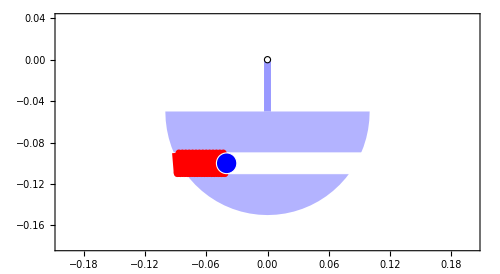

```mathematica
body1[φ_,x_] := Module[{b},
b=
{
(* СТЕРЖЕНЬ *)
Lighter[Blue, 0.6],Thickness[0.01],Line[{{0, 0}, {0, -0.05}}],
(* ПЛАСТИНА *)
Lighter[Blue, 0.7],Disk[{0, -0.05},0.1, {-180 °, 0 °}],
(* ОПОРА *)
White, EdgeForm[{Thick, Black}],Disk[{0, 0}, 0.003],
(* КАНАЛ *)
EdgeForm[{Thin, White}],Rectangle[{-1, -0.09}, {1, -0.11}],
(* ПРУЖИНА *)
Red,Thin,Translate[Line[Spring[x, 0.02, 30]],{-0.09,-0.1}],
(* ШАРИК *)
Blue,Disk[{-0.09+x,-0.1}, 0.01]
};
   GeometricTransformation[b, {RotationMatrix[φ], {0, 0}}]
   ];

Graphics[body1[0,0.05], Frame -> True,PlotRange->{{-0.2,0.2},{-0.18,0.04}},ImageSize->500]
```

## Интегрирование дифференциальных уравнений

-Graphics-

#### Положение шарика относительно системы координат O x_1 y_1 z_1, связанной с первым телом

Радиус-вектор точки А относительно системы Ox_1 y_1 z_1

```mathematica
Subscript[ρ, A]={-√(R^2-h^2),-2*h};
```

Радиус вектор точки М относительно точки А в системе координат Ox_1 y_1 z_1

```mathematica
Subscript[ρ, M]=Subscript[ρ, A]+{Subscript[l, 0]+x[t],0};
```

#### Положение шарика относительно неподвижной системы координат Oxyz

```mathematica
Subscript[r, M]=RotationMatrix[φ[t]].Subscript[ρ, M]
```

{2 h Sin[φ[t]]+Cos[φ[t]] (-√(-h^2+R^2)+l_0+x[t]),-2 h Cos[φ[t]]+Sin[φ[t]] (-√(-h^2+R^2)+l_0+x[t])}

#### Вектор абсолютной скорости шарика

```mathematica
Subscript[v, M]=D[Subscript[r, M],t]//FullSimplify
```

{Cos[φ[t]] x'[t]+(2 h Cos[φ[t]]+√(-h^2+R^2) Sin[φ[t]]-Sin[φ[t]] (l_0+x[t])) φ'[t],Sin[φ[t]] x'[t]+2 h Sin[φ[t]] φ'[t]+Cos[φ[t]] (-√(-h^2+R^2)+l_0+x[t]) φ'[t]}

### Кинетическая энергия

#### Кинетическая энергия шарика

```mathematica
Subscript[T, 2]=FullSimplify[Subscript[m, 2] Subscript[v, M].Subscript[v, M]/2]
```

1/2 m_2 (x'[t]^2+4 h x'[t] φ'[t]+(3 h^2+R^2-(2 √(-h^2+R^2)-l_0-x[t]) (l_0+x[t])) φ'[t]^2)

#### Кинетическая энергия первого тела (стержень + сектор)

Стержень длиной h,массой  m_11,вращающийся вокруг оси O. Момент инерции m_11 h^2/3

```mathematica
Subscript[T, 11]=(Subscript[m, 11] h^2/3)*φ'[t]^2/2;
```

Сектор, вращающийся вокруг оси  О

```mathematica
Subscript[J, 12]=1/2*(Subscript[m, 12] R^2)/2+Subscript[m, 12] h^2;
Subscript[T, 12]=(Subscript[J, 12]*φ'[t]^2)/2
```

1/2 (h^2 m_12+(R^2 m_12)/4) φ'[t]^2

#### Кинетическая энергия системы

```mathematica
Subscript[T, sys]=FullSimplify[Subscript[T, 11]+Subscript[T, 12]+Subscript[T, 2]]
```

1/24 ((4 h^2 m_11+3 (4 h^2+R^2) m_12) φ'[t]^2+12 m_2 (x'[t]^2+4 h x'[t] φ'[t]+(3 h^2+R^2-(2 √(-h^2+R^2)-l_0-x[t]) (l_0+x[t])) φ'[t]^2))

### Потенциальная энергия

#### Тело 2: шарик

Нулевой уровень - горизонтальная плоскость, проходящая через ось вращения O.
Потенциальная энергия шарика (координата y в неподвижной системе, умноженная на массу шарика и ускорение свободного падения.

```mathematica
Subscript[Π, g2]=Subscript[m, 2] *g *Subscript[r, M][[2]]
```

g m_2 (-2 h Cos[φ[t]]+Sin[φ[t]] (-√(-h^2+R^2)+l_0+x[t]))

Потенциальная энергия пружины

```mathematica
Subscript[Π, c2]=(c(x[t]-Subscript[l, 0])^2)/2;
```

#### Тело 1

Положение центра масс стержня и сектора относительно системы координат O x_1 y_1 z_1

```mathematica
Subscript[ρ, 1]=(Subscript[m, 11]{0,-h/2}+Subscript[m, 12]{0,-h-4 R/(3 π)})/(Subscript[m, 11]+Subscript[m, 12]);
```

Положение центра масс стержня и сектора относительно системы координат Oxyz

```mathematica
Subscript[r, 1]=RotationMatrix[φ[t]].Subscript[ρ, 1]
```

{-(Sin[φ[t]] (-(h m_11)/2+(-h-(4 R)/(3 π)) m_12))/(m_11+m_12),(Cos[φ[t]] (-(h m_11)/2+(-h-(4 R)/(3 π)) m_12))/(m_11+m_12)}

Координата y этого вектора будет высотой центра масс системы пластина + стержень относительно нулевого уровня энергии

```mathematica
Subscript[Π, g1]=(Subscript[m, 11]+Subscript[m, 12])*g*Subscript[r, 1][[2]]
```

g Cos[φ[t]] (-(h m_11)/2+(-h-(4 R)/(3 π)) m_12)

#### Потенциальная энергия системы

```mathematica
Subscript[Π, sys]=Subscript[Π, g2]+Subscript[Π, c2]+Subscript[Π, g1]
```

g Cos[φ[t]] (-(h m_11)/2+(-h-(4 R)/(3 π)) m_12)+1/2 c (-l_0+x[t])^2+g m_2 (-2 h Cos[φ[t]]+Sin[φ[t]] (-√(-h^2+R^2)+l_0+x[t]))

### Уравнения движения

```mathematica
eq1=FullSimplify[D[D[Subscript[T, sys],φ'[t]],t]-D[Subscript[T, sys],φ[t]]==-D[Subscript[Π, sys],φ[t]]]
```

m_12 (-4 g (3 h π+4 R) Sin[φ[t]]-3 π (4 h^2+R^2) φ''[t])+12 π m_2 (g √(-h^2+R^2) Cos[φ[t]]-2 g h Sin[φ[t]]+2 √(-h^2+R^2) x'[t] φ'[t]-2 h x''[t]-(3 h^2+R^2) φ''[t]-(l_0+x[t]) (g Cos[φ[t]]+2 x'[t] φ'[t]+(-2 √(-h^2+R^2)+l_0+x[t]) φ''[t]))==2 h π m_11 (3 g Sin[φ[t]]+2 h φ''[t])

```mathematica
eq2 = FullSimplify[D[D[Subscript[T, sys],x'[t]], t] - D[Subscript[T, sys], x[t]] ==- D[Subscript[Π, sys], x[t]]]
```

c x[t]+m_2 (g Sin[φ[t]]+(√(-h^2+R^2)-l_0-x[t]) φ'[t]^2+x''[t]+2 h φ''[t])==c l_0

Параметры системы

```mathematica
params={Subscript[m, 11]->1,Subscript[m, 12]->1,Subscript[m, 2]->0.3,R->1,Subscript[l, 0]->0.4,g->9.807,c->9.0,h->R/2};
```

Интегрирование

```mathematica
numEq={eq1,eq2,φ[0]==0.3,φ'[0]==0.3,x[0]==0,x'[0]==0}//.params
```

{-341.77 Sin[φ[t]]-6 π φ''[t]+11.3097 (8.49311 Cos[φ[t]]-9.807 Sin[φ[t]]+√3 x'[t] φ'[t]-x''[t]-(7 φ''[t])/4-(0.4+x[t]) (9.807 Cos[φ[t]]+2 x'[t] φ'[t]+(-1.33205+x[t]) φ''[t]))==π (29.421 Sin[φ[t]]+φ''[t]),9. x[t]+0.3 (9.807 Sin[φ[t]]+(0.466025-x[t]) φ'[t]^2+x''[t]+φ''[t])==3.6,φ[0]==0.3,φ'[0]==0.3,x[0]==0,x'[0]==0}

```mathematica
sol=NDSolve[numEq,{φ[t],φ'[t],x[t],x'[t]},{t,0,5}]//Flatten
```

{φ[t]→InterpolatingFunction[{{0., 5.}}, <>][t],φ'[t]→InterpolatingFunction[{{0., 5.}}, <>][t],x[t]→InterpolatingFunction[{{0., 5.}}, <>][t],x'[t]→InterpolatingFunction[{{0., 5.}}, <>][t]}

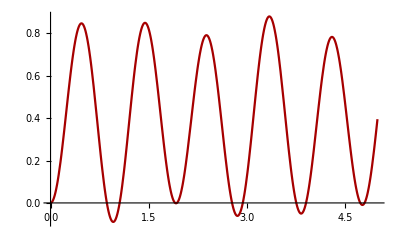

```mathematica
Plot[x[t]/.sol,{t,0,5}]
```

Проверка интеграла энергии

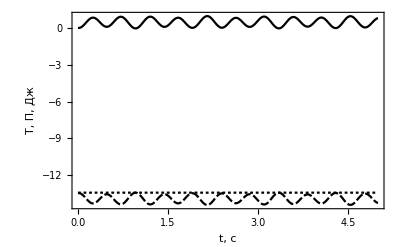

```mathematica
Plot[{Subscript[T, sys],Subscript[Π, sys],Subscript[T, sys]+Subscript[Π, sys]}//.params/.sol//Evaluate,{t,0.0,5.0},Frame->True,BaseStyle->14,FrameLabel->{"t, c"," T, Π, Дж"},PlotLegends->{"T","Π","T+Π"},PlotTheme->"Monochrome"]
```

## Рисуем систему

Рисуем систему в соответствии с параметрами в списке params

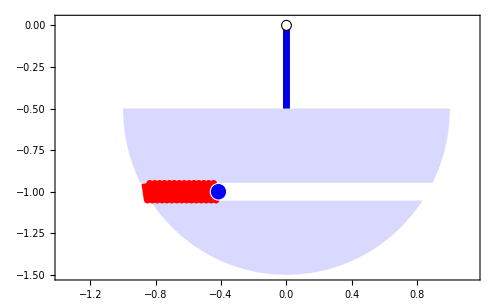

```mathematica
ClearAll[body1]
body1[φi_,xi_] := Module[{b,rshar=0.05,dpru=0.1},
b={(* СТЕРЖЕНЬ *)
Darker[Blue, 0.1],Thickness[0.01],Line[{{0, 0}, {0, -h}}],
(* ПЛАСТИНА *)
Lighter[Blue, 0.85],Disk[{0, -h},R, {-180 °, 0 °}],
(* ОПОРА *)
White, EdgeForm[{Thick, Black}],Disk[{0, 0}, 0.03],
(* КАНАЛ *)
EdgeForm[{Thin, White}],Rectangle[Subscript[ρ, A]+{-0.5,-dpru/2},Subscript[ρ, A]+{2R,dpru/2}],
(* ПРУЖИНА *)
Red,Thin,Translate[Line[Spring[x[t]+Subscript[l, 0],dpru, 30]],Subscript[ρ, A]],
(* ШАРИК *)
Blue,Disk[Subscript[ρ, M], rshar]
}/.{φ[t]->φi,x[t]->xi}//.params;
   GeometricTransformation[b, {RotationMatrix[φi], {0, 0}}]
   ];

Graphics[body1[0,0.05], Frame -> True,ImageSize->500]
```

## Анимация

```mathematica
Animate[
Graphics[
body1[φ[t],x[t]]/.sol/.t->ti,PlotRange->{{-1.6,1.6},{-1.7,0.2}},ImageSize->600
],
{ti,0,5,0.05},
DisplayAllSteps->True]
```

## Экспорт анимации

Анимацию можно сохранить в файл типа анимированный gif

Генерируем кадры: t от 0 до t_max с шагом 0.05 (100 кадров для 5 секунд) при помощи функции Table

```mathematica
aniTable=Table[
 Graphics[
body1[φ[t],x[t]]/.sol/.t->ti,PlotRange->{{-1.5,1.5},{-1.5,0.1}},ImageSize->600
],
 {ti, 0,5, 0.05}];
```

Первые пять кадров

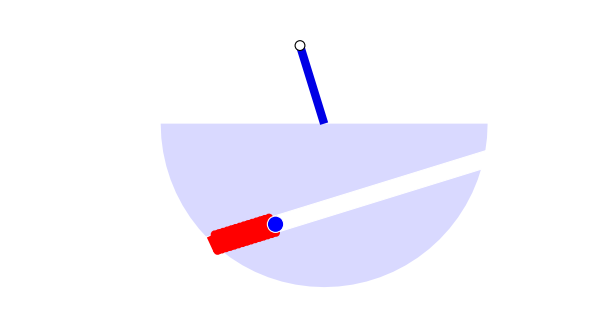
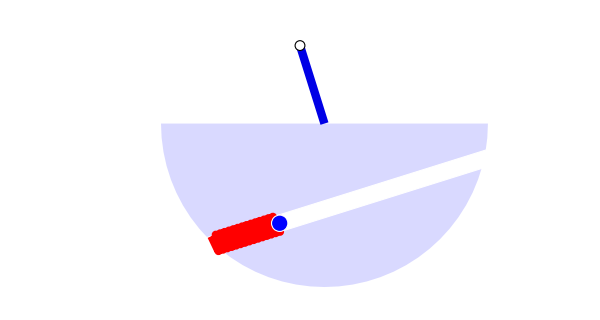
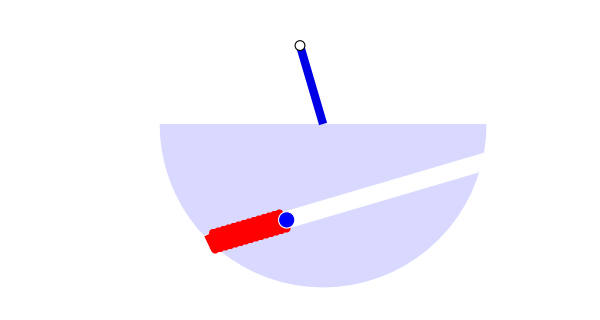
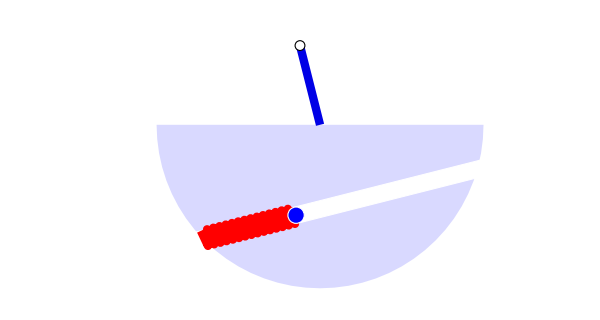

```mathematica
aniTable[[1;;4]]
```

## Экспорт

Для записи кадров в файл используем функцию Export

```mathematica
Export["animation.gif",aniTable]
```

animation.gif

Расширение имени файла (gif, avi) определит формат файла

```mathematica
Export["animation.avi",aniTable]
```

animation.avi

Файл получится большим, т.к. видео не сжато

## Экспорт

Чтобы создался файл поменьше попытаемся использовать сжатие (формат MPEG-4)

```mathematica
Export["animation.avi", aniTable,"VideoEncoding"->"MPEG-4 Video"]
```

animation.avi

Список форматов, поддерживаемых системой (Windows)

```mathematica
Internal`$VideoEncodings
```

{Uncompressed}

...сжатие не поддерживается -- только Uncompressed (несжатый).